```mathematica
Needs["OpenCLLink`"]
```

```mathematica
openclCode=ReadString[FileNameJoin[{NotebookDirectory[],"OpenCLMonteCarlo_BilayerGraphene.cl"}]];
```

```mathematica
rng=OpenCLFunctionLoad[openclCode,"RNGtest",{{"Float","Output"},{"Integer32","Input"}},100,"ShellOutputFunction"->Print];
values=ConstantArray[0,500];
seeds=RandomInteger[{362436000,562436000},500];
Mean[rng[values,seeds][[1]]]
StandardDeviation[rng[values,seeds][[1]]]
PearsonChiSquareTest[rng[values,seeds][[1]],UniformDistribution[]]
```

0.518201

0.293494

0.45021

```mathematica
(* Dimension units*)
EvToErg=1.6*10^-12;
k=1.38*10^-16 ;(*Boltzmann constant*)
c=3*10^10; (*Speed of light*)
T=100 ;(*Temperature*)
Subscript[D, ak]=18*EvToErg;(* Acoustic phonon constant*)
Subscript[D, opt]=1.4*10^9*EvToErg; (*Optic phonon constant*)
ℏ=10^-27 ;(* Dirak constant*)
ρ=2*7.7*10^-8 ;(* Surface dens*)
Subscript[v, s]=2.6*10^6 ;(* Speed of sound*)
e=4.8*10^-10 ;(* Electron charge*)
Subscript[v, f]=10^8 ;(* Speed of Fermi*)
Subscript[n, 0]=10^12; (* 2D concentration*)
Subscript[ϵ, ph]=0.196*EvToErg;(* Optic phonon energy*)
γ=0.35*EvToErg;
Δ=0.1*EvToErg; 
Subscript[Δ, 1]=Sqrt[γ^2/2+Δ^2];
Subscript[Δ, 2]=γ/Sqrt[2];
Subscript[Δ, 3]=Sqrt[γ^2+4 Δ^2];
Subscript[ν, ac]=(k*T*Subscript[D, ak])^2/(2*ℏ^3*ρ*Subscript[v, s]^2*Subscript[v, f]^2);
Subscript[ν, opt]=k*T*Subscript[D, opt]^2/(4*ℏ*ρ*Subscript[ϵ, ph]*Subscript[v, f]^2);
Subscript[ν, rad] = 1;
```

```mathematica
ω = 5 Subscript[ν, ac];
ϕ = π/6;
Subscript[E, x]=5;
Subscript[E, y]=5;
Subscript[E, xc]=0;
Subscript[E, yc]=0;
H = 0;
```

```mathematica
Subscript[H, SGS]=k*T*Subscript[ν, ac]*c/e/Subscript[v, f]^2;
Subscript[H, SI]=Subscript[H, SGS]/10000.0;
Subscript[E, SGS]=k*T*Subscript[ν, ac]/e/Subscript[v, f];
Subscript[E, SI]=Subscript[E, SGS]*300.0;
Subscript[j, SGS]=Subscript[n, 0]*Subscript[v, f]*e;
powerSGS=Subscript[j, SGS]*Subscript[E, SGS];
power0Etau=Subscript[n, 0]*e^2*Subscript[v, f]^2/γ;
```

```mathematica
n = 100;
fun=OpenCLFunctionLoad[openclCode,"jobKernel",{{"Float","Output"},{"Integer32","Output"},{"Integer32","Output"},{"Float","Input"},{"Integer32","Input"}},n];
values=Table[0,{i,n}];
numcols=Table[0,{i,n}];
upcols=Table[0,{i,n}];
params=Table[0,{i,19}];
```

```mathematica
outmas={};
VarName="Ex";
IterMessage="Solve is run!";
Dynamic[IterMessage]
gb=AbsoluteTime[];
For[var=0,var≤10,var+=0.5,
b=AbsoluteTime[];
(*Parameters*)
params[[1]]=Subscript[E, xc] / Subscript[E, SGS];(*Exc*)
params[[2]]=Subscript[E, yc]/Subscript[E, SGS];(*Eyc*)
params[[3]]=var/Subscript[E, SGS];(*Ex*)
params[[4]]=Subscript[E, y]/Subscript[E, SGS];(*Ey*)
params[[5]]=H/Subscript[H, SGS];(*H*)
params[[6]]=ω/Subscript[ν, ac];(*wx*)
params[[7]]=ω/Subscript[ν, ac];(*wy*)
params[[8]]=ϕ;(*phi*)
params[[9]]=1;(*wla_max*)
params[[10]]=Subscript[ν, opt]/Subscript[ν, ac];(*wlo_max*)
params[[11]]=Subscript[ν, rad]/Subscript[ν, ac];(*light_max*)
params[[12]]=Subscript[ϵ, ph]/k/T;(*Subscript[ℏω, 0]*)
params[[13]]=ℏ*ω/k/T;(*ℏω*)
params[[14]]=Subscript[Δ, 1]/k/T;(*Subscript[Δ, 1]*)
params[[15]]=Subscript[Δ, 2]/k/T;(*Subscript[Δ, 2]*)
params[[16]]=Subscript[Δ, 3]/k/T;(*Subscript[Δ, 3]*)
params[[17]]=Min[0.001/Max[params[[1;;5]]], 0.1/params[[6]]];(*step_time*)
params[[18]]=100000 * params[[17]];(*all_time*)
params[[19]]=ℏ/k/T/10^-13;(*Δϵ поиграться с ней*)
(*Solve*)
count=20;
out={};
Do[
seeds=RandomInteger[{100000000,1000000000},n];
res=fun[values,numcols,upcols,params,seeds];
AppendTo[out,res];
,{k,count}
];
res=Mean[out];
tau=params[[18]]/Mean[res[[2]]]/Subscript[ν, ac];
power0=power0Etau*tau*(params[[3]]*Subscript[E, SGS])^2;
Omega=2*e*Subscript[v, f]^2*h/c/γ;
AppendTo[outmas,{var,Mean[res[[1]]],Mean[res[[2]]],Mean[res[[3]]],StandardDeviation[res[[1]]],Δ/γ,γ/k/T,Omega,tau,(params[[6]]+params[[7]])/2*Subscript[ν, ac]}];
e=AbsoluteTime[];
IterMessage=VarName<>" = "<>ToString[N[var]]<>" solve for "<>ToString[e-b]<>" second(s)";
];
ge=AbsoluteTime[];
IterMessage="Solve is over for "<>ToString[ge-gb]<>" second(s)";
```

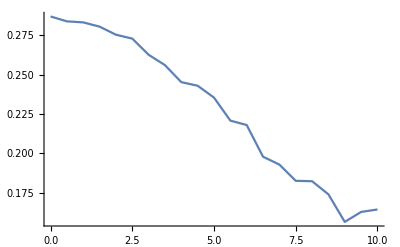

```mathematica
ListPlot[{outmas[[All,1;;2]]},Joined->True,InterpolationOrder->1,PlotRange->All]
```

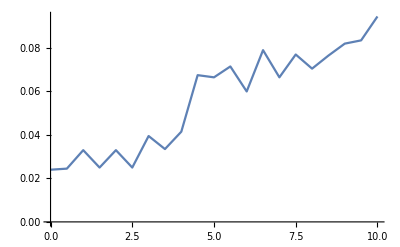

```mathematica
ListLinePlot[ outmas[[All,{1,4}]],Joined->True,InterpolationOrder->1,PlotRange->All]
```

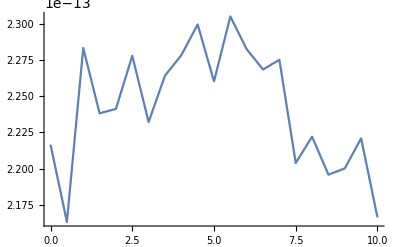

```mathematica
ListLinePlot[outmas[[All,{1,9}]],Joined->True,InterpolationOrder->1,PlotRange->All]
```

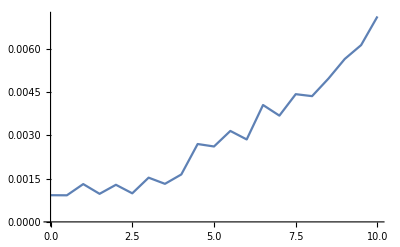

```mathematica
ListLinePlot[Transpose[{outmas[[All,1]],outmas[[All,4]]/outmas[[All,3]]}],Joined->True,InterpolationOrder->1,PlotRange->All]
```